## Convergencia numérica

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
colors={Blue,Red}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255]
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[0, 0, 1],RGBColor[1, 0, 0]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

RGBColor[Rational[10, 17], Rational[40, 51], Rational[4, 17]]

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ sunsetColors),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
  
plotPolarStyling = {PlotMarkers->{"●",4.5},
    PlotStyle -> (Directive[#, Thickness[0.002]] & /@ colors2),
    PlotRange -> 270, 
    Joined->True,
    PolarAxes -> True,
    PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
    PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100,150}},
    GridLinesStyle -> Directive[Gray, Dashed],
 
 BaseStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
 ImagePadding->{{5,5},{5,5}}};
  
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\4-Resultados"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\4-Resultados

## Eritrocito sano

### Convergencia numérica

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,1.46738}}

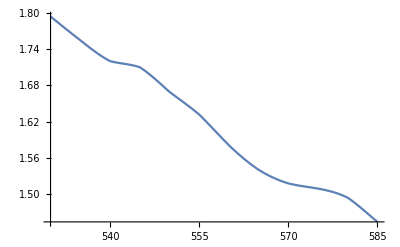

```mathematica
Plot[hola[x],{x,530,585}]
```

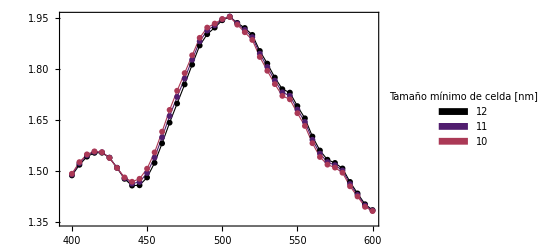

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

### Propiedades ópticas

#### Importación y preparación de datos

```mathematica
dataEriSano=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_Cabs_Csca.csv"];
dataQabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]/(Pi*2680^2)}];
dataQscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]/(Pi*2680^2)}];

dataEriSanoFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_440.csv"];

dataThetaEriSano=Drop[dataEriSanoFF440,1][[All,1]];
dataPhiEriSano=Drop[dataEriSanoFF440,1][[All,2]];
dataRCSEriSano=Drop[dataEriSanoFF440,1][[All,3]];

data440 = Transpose[{dataThetaEriSano *Pi/180, dataPhiEriSano*Pi/180, dataRCSEriSano}];
fInterp440 = Interpolation[data440,InterpolationOrder->1];
min440 = Min[dataRCSEriSano];
max440 = Max[dataRCSEriSano];
```

#### Gráficas

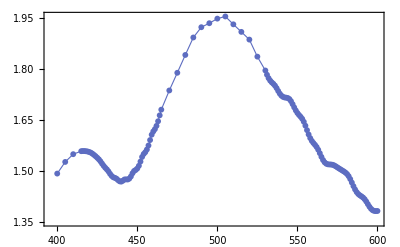

```mathematica
ListPlot[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],PlotMarkers->{"●",6},
                      Joined->True,
                      PlotStyle -> (Directive[colors[[2]], Thickness[0.002]]),
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
dataFF4400=Table[{th,fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/120}];
dataFF44000=Table[{th,fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/120}];
```

```mathematica
polarplot440FF=ListPolarPlot[{dataFF4400,dataFF44000},
              PlotRange->170,
              PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
              PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 40, 80}},
              PlotLegends->Placed[{Style[MaTeX["\\phi=0"],Magnification->1.2,Black],
                                  Style[MaTeX["\\phi=\\pi"],Magnification->1.2]},{0.85,0.9}],
              Evaluate[Sequence @@ plotPolarStyling]]
```

-Graphics-

```mathematica
Export["polarplot440FF.svg",polarplot440FF]
```

polarplot440FF.svg

```mathematica
plot2=ParametricPlot3D[
 {
  fInterp440[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Cos[ph*Pi/180],
  fInterp440[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Sin[ph*Pi/180],
  fInterp440[th*Pi/180, ph*Pi/180]*Cos[th*Pi/180]
 },
 {th, 0, 180},
 {ph, 0, 360},

ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["Rainbow"][
    Rescale[
      fInterp440[th*Pi/180, ph*Pi/180],
      {min440,max440}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 
 PlotPoints -> 50,
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
 PlotLegends -> BarLegend[
  {ColorData["Rainbow"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min440, max440, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.4]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4},
   
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
]
```

InterpolatingFunction::dmval: Input value {3.17333×10^-8,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0317333,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0634665,6.28319} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["FFdistribution0.svg",plot20,"AllowRasterization" -> False]
```

FFdistribution0.svg

```mathematica
Export["grafica_editable.svg", graficaFinal, ]
```

## Eritrocito sano

### Convergencia numérica

```mathematica
dataEriSanoCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Cabs_12_11_10.csv"];
dataEriSanoCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Eritrocito_sano_Csca_12_11_10.csv"];

dataQabsEriSano=Transpose[{dataEriSanoCabs[[All,1]],dataEriSanoCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEriSano=Transpose[{dataEriSanoCsca[[All,1]],dataEriSanoCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

```mathematica
hola=Interpolation[Transpose[{dataEriSanoCabs[[All,1]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]][[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
MinimalBy[Table[{x,hola[x]},{x,430,450}],Last]
```

{{440,1.46738}}

```mathematica
Plot[hola[x],{x,530,585}]
```

-Graphics-

```mathematica
plotEriSano=ListPlot[dataQext[dataQabsEriSano[[#]],dataQscaEriSano[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

-Graphics-

### Propiedades ópticas

```mathematica
dataEriSano=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_Cabs_Csca.csv"];
dataQabsEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,2]]/(Pi*2680^2)}];
dataQscaEriSanoFinal=Transpose[{dataEriSano[[All,1]],dataEriSano[[All,3]]/(Pi*2680^2)}];

dataEriSanoFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Eritrocito_sano_farfield_440.csv"];

dataThetaEriSano=Drop[dataEriSanoFF440,1][[All,1]];
dataPhiEriSano=Drop[dataEriSanoFF440,1][[All,2]];
dataRCSEriSano=Drop[dataEriSanoFF440,1][[All,3]];
```

```mathematica
(* columnas *)
x = dataEriSanoEF440[[All, 1]];
y = dataEriSanoEF440[[All, 2]];

ExRe = dataEriSanoEF440[[All, 4]];
ExIm = dataEriSanoEF440[[All, 5]];
EyRe = dataEriSanoEF440[[All, 6]];
EyIm = dataEriSanoEF440[[All, 7]];
EzRe = dataEriSanoEF440[[All, 8]];
EzIm = dataEriSanoEF440[[All, 9]];

(* magnitud del campo *)
Emag = Sqrt[
  ExRe^2 + ExIm^2 +
  EyRe^2 + EyIm^2 +
  EzRe^2 + EzIm^2
]
```

```mathematica
Min[Emag]
```

0.678489

```mathematica
f[-1598,-1509]
```

f[-1598,-1509]

```mathematica
Sqrt[
  0.16427^2 + -0.9526422^2 +
  -0.0009494^2 + 0.0022271^2 +
  -0.0098253^2 + 0.041219886^2
]
```

0.+0.937516 ⅈ

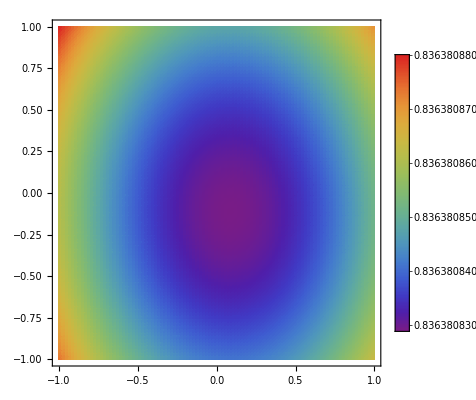

```mathematica
dataPlot = Transpose[{x, y, Emag}];
f = Interpolation[dataPlot];

DensityPlot[
 f[x, y],
 {x, Min[x], Max[x]},
 {y, Min[y], Max[y]},

 PlotPoints -> 100,
 MaxRecursion -> 2,
 ColorFunction -> "Rainbow",
 PlotLegends -> BarLegend[Automatic]
]
```

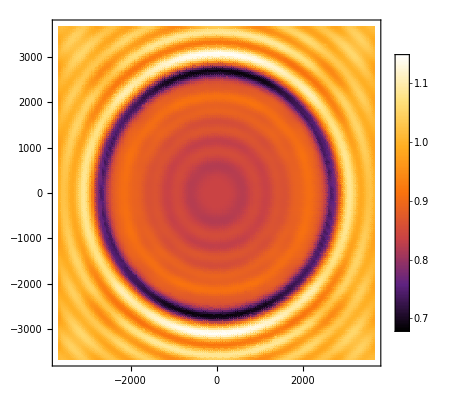

```mathematica
ListDensityPlot[
 dataPlot,

 
 ColorFunction -> "SunsetColors",
 PlotLegends -> BarLegend[Automatic],

 Mesh -> None,
 Frame -> True,
 AspectRatio -> 1
]
```

```mathematica
data440 = Transpose[{dataThetaEriSano *Pi/180, dataPhiEriSano*Pi/180, dataRCSEriSano}];
fInterp440 = Interpolation[data440,InterpolationOrder->1];
min440 = Min[dataRCSEriSano[[1]]];
max440 = Max[dataRCSEriSano[[1]]];
```

```mathematica
fInterp440[2*Pi/180,180*Pi/180]
```

92.8

```mathematica
PolarPlot[{
 fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi]}, {th, 0, 2 Pi},
 Mesh->355/5,
 (* Ajustes de visualización para que sea igual a CST *)
 PlotStyle -> {{Red, Thickness[0.002]},{Blue, Thickness[0.002]}},
 PlotRange -> 150, (* Suficiente para el máximo de 107.6 dB *)
 
 (* Configuración de ejes y etiquetas *)
 PolarAxes -> True,
 PolarTicks -> {"Degrees", Automatic},
 PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100}},
 GridLinesStyle -> Directive[Gray, Dashed]

]
```

-Graphics-

```mathematica
ParametricPlot3D[
 {
  fInterp440[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Cos[ph*Pi/180],
  fInterp440[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Sin[ph*Pi/180],
  fInterp440[th*Pi/180, ph*Pi/180]*Cos[th*Pi/180]
 },
 {th, 0, 180},
 {ph, 0, 360},

ColorFunction -> Function[{x, y, z, th, ph},
  ColorData["Rainbow"][
    Rescale[fInterp440[th*Pi/180, ph*Pi/180], {min, max}]
  ]
],
ColorFunctionScaling -> False,
 
 PlotPoints -> 200,

 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 AxesOrigin -> {0, 0, 0},
 PlotRange -> All,
 Lighting -> "Neutral",
 


PlotLegends -> BarLegend[
  {ColorData["Rainbow"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440, max440}], #} & /@ 
     Subdivide[min, max, 5] )
]
]
```

InterpolatingFunction::dmval: Input value {1.57869×10^-8,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0157869,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0315738,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
ParametricPlot3D[
 {
  fInterp540[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Cos[ph*Pi/180],
  fInterp540[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Sin[ph*Pi/180],
  fInterp540[th*Pi/180, ph*Pi/180]*Cos[th*Pi/180]
 },
 {th, 0, 180},
 {ph, 0, 360},

ColorFunction -> Function[{x, y, z, th, ph},
  ColorData["Rainbow"][
    Rescale[fInterp540[th*Pi/180, ph*Pi/180], {min, max}]
  ]
],
ColorFunctionScaling -> False,
 
 PlotPoints -> 200,

 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 AxesOrigin -> {0, 0, 0},
 PlotRange -> All,
 Lighting -> "Neutral",
 


PlotLegends -> BarLegend[
  {ColorData["Rainbow"], {0, 1}},
  Ticks -> ( {Rescale[#, {min540, max540}], #} & /@ 
     Subdivide[min, max, 5] )
]
]
```

InterpolatingFunction::dmval: Input value {1.57869×10^-8,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0157869,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0315738,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
PolarPlot[{
 fInterp540[Abs[If[th > Pi, th - 2 Pi, th]], 0],fInterp540[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0, 2 Pi},
 
 (* Ajustes de visualización para que sea igual a CST *)
 PlotStyle -> {{Red, Thickness[0.002]},{Blue, Thickness[0.002]}},
 PlotRange -> 150, (* Suficiente para el máximo de 107.6 dB *)
 
 (* Configuración de ejes y etiquetas *)
 PolarAxes -> True,
 PolarTicks -> {"Degrees", Automatic},
 PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100}},
 GridLinesStyle -> Directive[Gray, Dashed]

]
```

-Graphics-

```mathematica
ParametricPlot3D[
 {
  fInterp575[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Cos[ph*Pi/180],
  fInterp575[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Sin[ph*Pi/180],
  fInterp575[th*Pi/180, ph*Pi/180]*Cos[th*Pi/180]
 },
 {th, 0, 180},
 {ph, 0, 360},

ColorFunction -> Function[{x, y, z, th, ph},
  ColorData["Rainbow"][
    Rescale[fInterp575[th*Pi/180, ph*Pi/180], {min, max}]
  ]
],
ColorFunctionScaling -> False,
 
 PlotPoints -> 200,

 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 AxesOrigin -> {0, 0, 0},
 PlotRange -> All,
 Lighting -> "Neutral",
 


PlotLegends -> BarLegend[
  {ColorData["Rainbow"], {0, 1}},
  Ticks -> ( {Rescale[#, {min575, max575}], #} & /@ 
     Subdivide[min, max, 5] )
]
]
```

InterpolatingFunction::dmval: Input value {1.57869×10^-8,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0157869,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0315738,6.22004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
PolarPlot[{
 fInterp575[Abs[If[th > Pi, th - 2 Pi, th]], 0],fInterp575[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0, 2 Pi},
 
 (* Ajustes de visualización para que sea igual a CST *)
 PlotStyle -> {{Red, Thickness[0.002]},{Blue, Thickness[0.002]}},
 PlotRange -> 150, (* Suficiente para el máximo de 107.6 dB *)
 
 (* Configuración de ejes y etiquetas *)
 PolarAxes -> True,
 PolarTicks -> {"Degrees", Automatic},
 PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 50, 100}},
 GridLinesStyle -> Directive[Gray, Dashed]

]
```

-Graphics-

```mathematica
N[15*Pi/180]
```

0.261799

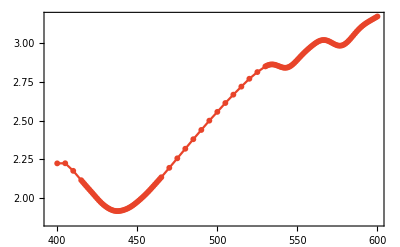

```mathematica
ListPlot[dataQext[dataQabsEriSanoFinal,dataQscaEriSanoFinal],PlotMarkers->{"●",6},
                      Joined->True,
                      PlotStyle->colors2,
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Plot3D
```

Plot3D

## Esferocito

```mathematica
dataEsfFF440=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_farfield_440.csv"];

dataThetaEsf=Drop[dataEsfFF440,1][[All,1]];
dataPhiEsf=Drop[dataEsfFF440,1][[All,2]];
dataRCSEsf=Drop[dataEsfFF440,1][[All,3]];

data440Esf = Transpose[{dataThetaEsf *Pi/180, dataPhiEsf*Pi/180, dataRCSEsf}];
fInterp440Esf = Interpolation[data440Esf,InterpolationOrder->1];
min440Esf = Min[dataRCSEsf];
max440Esf = Max[dataRCSEsf];
```

```mathematica
dataFF4400EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/120}];
dataFF44000EsfDif=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]-fInterp440[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/120}];

dataFF4400Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], 0]}, {th, 0,  2 Pi, 2 Pi/120}];
dataFF44000Esf=Table[{th,fInterp440Esf[Abs[If[th > Pi, th - 2 Pi, th]], Pi/2]}, {th, 0,  2 Pi, 2 Pi/120}];
```

```mathematica
polarplot440FFEsfDif=ListPolarPlot[{dataFF4400EsfDif,dataFF44000EsfDif},
              PlotRange->80,
              PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
              PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 10,20,30,40}},
              PlotLegends->Placed[{Style[MaTeX["\\phi=0"],Magnification->1.2,Black],
                                  Style[MaTeX["\\phi=\\pi"],Magnification->1.2]},{0.85,0.9}],
              Evaluate[Sequence @@ plotPolarStyling]]
              
polarplot440FFEsf=ListPolarPlot[{dataFF4400Esf,dataFF44000Esf},
              PlotRange->170,
              PolarTicks -> {Drop[Table[i, {i, 0, 2 Pi, Pi/6}], -1], Automatic},
              PolarGridLines -> {Table[a Degree, {a, 0, 360, 30}], {0, 40, 80}},
              PlotLegends->Placed[{Style[MaTeX["\\phi=0"],Magnification->1.2,Black],
                                  Style[MaTeX["\\phi=\\pi"],Magnification->1.2]},{0.85,0.9}],
              Evaluate[Sequence @@ plotPolarStyling]]
```

-Graphics-

-Graphics-

```mathematica
Export["polarplot440FFEsf.svg",polarplot440FFEsf]
Export["polarplot440FFEsfDif.svg",polarplot440FFEsfDif]
```

polarplot440FFEsf.svg

polarplot440FFEsfDif.svg

```mathematica
plot2=ParametricPlot3D[
 {
  fInterp440Esf[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Cos[ph*Pi/180],
  fInterp440Esf[th*Pi/180, ph*Pi/180]*Sin[th*Pi/180]*Sin[ph*Pi/180],
  fInterp440Esf[th*Pi/180, ph*Pi/180]*Cos[th*Pi/180]
 },
 {th, 0, 180},
 {ph, 0, 360},

ColorFunction -> Function[{x,y,z,th,ph},

   ColorData["Rainbow"][
    Rescale[
      fInterp440Esf[th*Pi/180, ph*Pi/180],
      {min440Esf,max440Esf}
    ]
   ]

 ],
 ColorFunctionScaling -> False,
 
 PlotPoints -> 150,
 Boxed -> True,
 Axes -> True,
 AxesLabel -> {"x", "y", "z"},
 PlotRange -> All,
 
 Mesh->False,
 
 PlotLegends -> BarLegend[
  {ColorData["Rainbow"], {0, 1}},
  Ticks -> ( {Rescale[#, {min440Esf, max440Esf}], #} & /@ 
     Subdivide[min440Esf, max440Esf, 5] )
,LegendLabel->Style[MaTeX["\\text{dB}\\:[\\mbox{nm}^2]"],Magnification->1.4]],

   LabelStyle->{Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4},
   
   
   ViewPoint -> {-5, 1, 2}, 
  ViewVertical -> {0, 1, 0}
]
```

InterpolatingFunction::dmval: Input value {2.10845×10^-8,6.24102} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0210845,6.24102} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.042169,6.24102} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
ListPlot[dataQext[dataQabsEsfFinal,dataQscaEsfFinal],PlotMarkers->{"●",6},
                      Joined->True,
                      PlotStyle->colors2,
                      FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Evaluate[Sequence @@ plotStyling]]
```

-Graphics-

```mathematica
dataQext[dataQabsEsfFinal,dataQscaEsfFinal]
```

{{400,2.22487},{405,2.22549},{410,2.17673},{415,2.11611},{416,2.104},{417,2.09197},{418,2.08008},{419,2.06834},{420,2.0567},{421,2.04507},{422,2.03335},{423,2.02153},{424,2.00968},{425,1.99797},{426,1.98663},{427,1.9759},{428,1.96594},{429,1.95684},{430,1.94863},{431,1.94128},{432,1.93477},{433,1.92915},{434,1.92449},{435,1.92089},{436,1.91844},{437,1.91716},{438,1.91702},{439,1.91791},{440,1.9197},{441,1.92227},{442,1.92553},{443,1.92945},{444,1.93406},{445,1.9394},{446,1.94549},{447,1.9523},{448,1.95978},{449,1.96779},{450,1.97624},{451,1.985},{452,1.99402},{453,2.0033},{454,2.01287},{455,2.02278},{456,2.03307},{457,2.04373},{458,2.05472},{459,2.06597},{460,2.07737},{461,2.08885},{462,2.10036},{463,2.1119},{464,2.12348},{465,2.13518},{470,2.19612},{475,2.25751},{480,2.31929},{485,2.38075},{490,2.44059},{495,2.50055},{500,2.55721},{505,2.61427},{510,2.66817},{515,2.72},{520,2.77078},{525,2.81391},{530,2.85048},{531,2.8558},{532,2.85987},{533,2.86247},{534,2.86347},{535,2.86288},{536,2.86085},{537,2.85767},{538,2.85376},{539,2.84965},{540,2.84589},{541,2.84304},{542,2.84158},{543,2.84188},{544,2.84416},{545,2.84847},{546,2.85472},{547,2.86267},{548,2.87199},{549,2.88228},{550,2.89316},{551,2.90427},{552,2.91532},{553,2.9261},{554,2.9365},{555,2.94649},{556,2.95607},{557,2.96529},{558,2.97418},{559,2.98273},{560,2.99087},{561,2.99848},{562,3.00534},{563,3.01125},{564,3.01593},{565,3.01918},{566,3.0208},{567,3.02072},{568,3.01896},{569,3.01568},{570,3.01117},{571,3.00581},{572,3.00009},{573,2.99455},{574,2.98974},{575,2.98614},{576,2.98421},{577,2.98425},{578,2.98646},{579,2.99089},{580,2.99743},{581,3.00587},{582,3.01589},{583,3.02708},{584,3.03903},{585,3.0513},{586,3.06351},{587,3.07533},{588,3.0865},{589,3.09686},{590,3.10635},{591,3.11497},{592,3.12279},{593,3.12995},{594,3.13659},{595,3.14286},{596,3.14892},{597,3.15487},{598,3.16081},{599,3.16676},{600,3.17274}}

```mathematica
dataEsfCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Cabs_12_11_10.csv"];
dataEsfCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esferocito_Csca_12_11_10.csv"];

dataQabsEsf=Transpose[{dataEsfCabs[[All,1]],dataEsfCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
dataQscaEsf=Transpose[{dataEsfCsca[[All,1]],dataEsfCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,4];
```

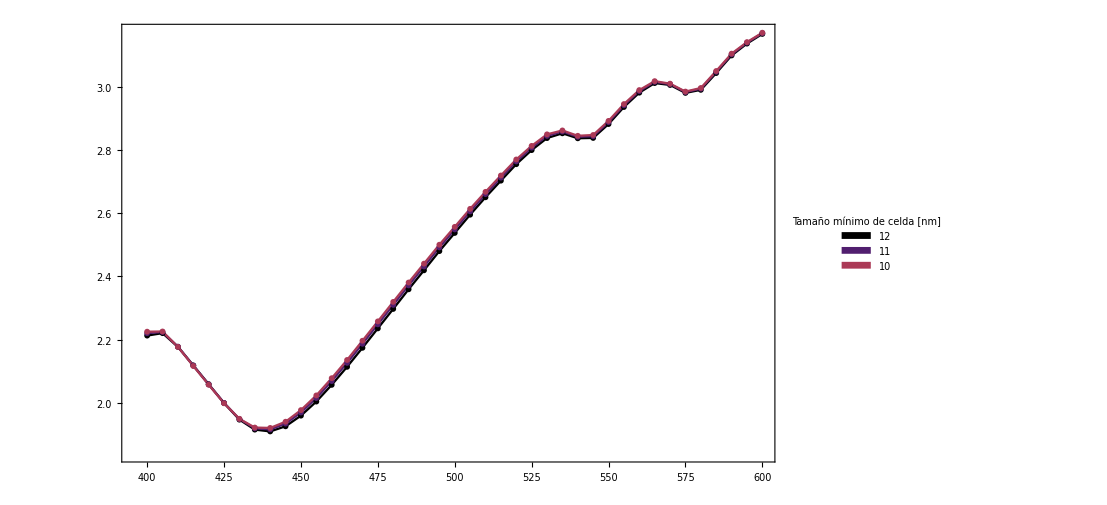

```mathematica
plotEsferocito=ListPlot[dataQext[dataQabsEsf[[#]],dataQscaEsf[[#]]]&/@Range[1,3],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"12","11","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.5,0.2}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

Part::partd: Part specification dataQabsMeshLocal⟦3⟧ is longer than depth of object.

Part::partd: Part specification dataQscaMeshLocal⟦3⟧ is longer than depth of object.

Part::partd: Part specification dataQabsMeshLocal⟦3⟧⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

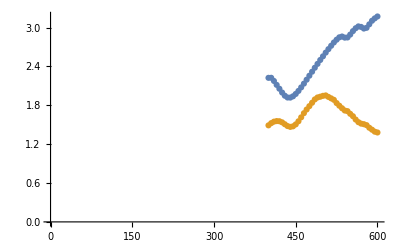

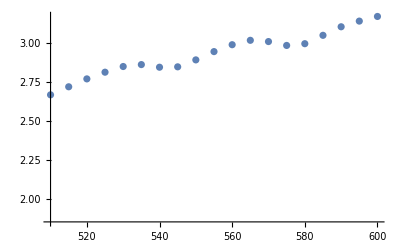

```mathematica
ListPlot[{dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]],dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]],dataQext[dataQabsMeshLocal[[3]],dataQscaMeshLocal[[3]]]}]
ListPlot[{dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]]},PlotRange->{{510,600},{Automatic,Automatic}}]
```

```mathematica
dataQext[dataQabsEsf[[3]],dataQscaEsf[[3]]]
```

{{400,2.22487},{405,2.22549},{410,2.17673},{415,2.11611},{420,2.0567},{425,1.99797},{430,1.94863},{435,1.92089},{440,1.9197},{445,1.9394},{450,1.97624},{455,2.02278},{460,2.07737},{465,2.13518},{470,2.19612},{475,2.25751},{480,2.31929},{485,2.38075},{490,2.44059},{495,2.50055},{500,2.55721},{505,2.61427},{510,2.66817},{515,2.72},{520,2.77078},{525,2.81391},{530,2.85048},{535,2.86288},{540,2.84589},{545,2.84847},{550,2.89316},{555,2.94649},{560,2.99087},{565,3.01918},{570,3.01117},{575,2.98614},{580,2.99743},{585,3.0513},{590,3.10635},{595,3.14286},{600,3.17274}}

```mathematica
MinimalBy[dataQext[dataQabsEriSano[[3]],dataQscaEriSano[[3]]],Last]
```

{{600,1.38098}}

## Microcito

## Macrocito